-Graphics-

Make: Matrices & Geometry
Authors:  Bill Davis and Jerry Uhl  ©1996-2010
Publisher:  Make: Mathematics

# MGM.02 2D Matrix Action LITERACY

Mathematica 8.0 Initializations

```mathematica
Off[General::"spell"];
  Off[General::"spell1"];  
Off[SingularValues::"deprec"];  

Needs["Units`"];  

SetOptions[ListAnimate, AnimationRepetitions -> 4];  
SetOptions[Animate, AnimationRepetitions -> 4];  
CMView={2.7,1.6,1.2};
```

#### Vector Drawer

```mathematica
(* :Date:  Copyright 1993-2011, Math Everywhere, Inc. 
*)
(*
Original Conception to create a vector drawer is due to Bill Davis.
Current code is by Bruce Carpenter.
*)
(*  :Drawbacks:  Since the vectors are drawn out of 
     context, the shapes of the arrowheads are only 
     correct with AspectRatio set to Automatic.
*)
```

```mathematica
BeginPackage["Vector3D`"];
```

```mathematica
Axes3D::usage="Axes3D[a, b] creates a Graphics3D object of cartesian axes with x, y, and z running from -a/3 to a, and with axes labels b units beyond the tips of the axes.  Axes3D[a] is Axes3D[a, a/8].";
Perpend::usage="Perpend[a] returns a unit vector which is perpendicular to the vector a.";
Vector::usage="Vector[a] produces a 2 or 3 dimensional vector from the origin to a. Arrow[a, Tail → tail] gives a vector from tail to a.";
CandMArrow::usage="CandMArrow[a, b] gives a 2D or 3D arrow from a to b.";
VectorHead::usage="VectorHead[a, vec] produces an arrowhead with its tip placed at the point a, pointing in the direction of the vector vec.";
Tail::usage="Tail → point puts the tail of the vector at point.";
Aperture::usage="Aperture is the ratio of the radius of the base to the length of the head of a vector.";
TipSize::usage="TipSize specifies an absolute size for the inner tip length of the head of a vector.";
TipRatio::usage="TipRatio is the ratio of the inner length of the arrowhead to the length of the shaft of a vector.";
HeadRatio::usage="HeadRatio is the ratio of the outer length of the arrowhead to the length of the shaft of a vector.";
HeadSize::usage="HeadSize specifies an absolute size for the head of a vector.";
ScaleFactor::usage="ScaleFactor specifies the amount to scale a vector in length and may be either a number or a pure function.";
ZeroVectorPointSize::usage="ZeroVectorPointSize is the size of the point used to represent a zero vector.";
Options[Vector]=Options[CandMArrow]=Options[VectorHead]={HeadRatio->0.18,TipRatio->0.14,Aperture->0.3,ScaleFactor->1,HeadType->Polygon,ShaftQ->True,EdgesQ->True,VectorColor->RGBColor[0,0,1],ShaftWidth->0.005,ZeroVectorPointSize->0.01};
Begin["`Private`"];
SetOptions[ParametricPlot,AspectRatio->Automatic];
SetOptions[Plot,AspectRatio->Automatic];
SetOptions[Graphics,AspectRatio->Automatic];
Axes3D[u_,v_]:=Graphics3D[{{Blue,Line[{{-u/3,0,0},{u,0,0}}]},Text["x",{u+v,0,0}],{Blue,Line[{{0,-u/3,0},{0,u,0}}]},Text["y",{0,u+v,0}],{Blue,Line[{{0,0,-u/3},{0,0,u}}]},Text["z",{0,0,u+v}]}];
Axes3D[u_]:=Axes3D[u,u/8];
Perpend[a_?VectorQ]:=Normalize[{a⟦2⟧,-a⟦1⟧}]/;Length[a]==2;
Perpend[a_?VectorQ]:=Normalize[If[a⟦1⟧==0,{1,0,0},{a⟦2⟧,-a⟦1⟧,0}]]/;Length[a]==3;
Base3D=Table[{Cos[(2 k π)/8.],Sin[(2 k π)/8.]},{k,0,8}];
CandMArrow[from_?VectorQ,to_?VectorQ,opts___]:=Module[{sq,sw,ht,hs,hr,tr,ap,sf,vc,zvps,diff=to-from,tip},{sq,sw,ht,hs,hr,ts,tr,ap,sf,vc,zvps}={ShaftQ,ShaftWidth,HeadType,HeadSize,HeadRatio,TipSize,TipRatio,Aperture,ScaleFactor,VectorColor,ZeroVectorPointSize}/.{opts}/.Options[Vector];If[from==to,Return[Graphics[{PointSize[zvps],vc,Point[from]}]]];diff=If[NumberQ[N[sf]],sf diff,sf[diff]];tip=from+diff;If[NumberQ[hs],hr=hs/Norm[diff];tr=0.75 hr];If[NumberQ[ts],tr=ts/Norm[diff]];Graphics[{If[sq,{vc,Thickness[sw],Line[{from,tip-tr diff}]},{}],With[{trans=ap hr Norm[diff] Perpend[diff]},{vc,Thickness[sw],ht[{tip,tip-hr diff+trans,tip-tr diff,tip-hr diff-trans,tip}]}]}]]/;Length[from]==Length[to]==2
CandMArrow[from_?VectorQ,to_?VectorQ,opts___]:=Module[{sq,eq,sw,hs,hr,tr,ap,sf,vc,zvps,diff=to-from,tip},{sq,eq,sw,hs,hr,ap,sf,vc,zvps}={ShaftQ,EdgesQ,ShaftWidth,HeadSize,HeadRatio,Aperture,ScaleFactor,VectorColor,ZeroVectorPointSize}/.{opts}/.Options[Vector];If[from==to,Return[Graphics3D[{PointSize[zvps],vc,Point[from]}]]];diff=If[NumberQ[N[sf]],sf diff,sf[diff]];tip=from+diff;If[NumberQ[hs],hr=hs/Norm[diff]];tr=hr/2;Graphics3D[{If[sq,{vc,Thickness[sw],Line[{from,tip-tr diff}]},{}],If[eq,{},EdgeForm[]],{SurfaceColor[vc],With[{temp=Perpend[diff]},(Polygon[Append[#1,tip]]&)/@Partition[(tip-hr diff+#1&)/@((ap hr Norm[diff] Base3D).{temp,Normalize[temp×diff]}),2,1]]}}]]/;Length[from]==Length[to]==3
Vector[a_,Tail->b_,opts___]:=CandMArrow[b,a+b,opts]
Vector[a_,opts___]:=CandMArrow[Table[0,{Length[a]}],a,opts]
VectorHead[a_,b_,opts___]:=CandMArrow[a-b,a,ShaftQ->False,opts];
End[];
EndPackage[];
```

```mathematica
Graphics`Colors`GosiaGreen=RGBColor[0, 0.392187, 0];
```

#### ThreeAxes[u,v]

```mathematica
ThreeAxes[u_,v_]:=Graphics3D[{{Blue,Line[{{-u,0,0},{u,0,0}}]},Text["x",{u+v,0,0}],{Blue,Line[{{0,-u,0},{0,u,0}}]},Text["y",{0,u+v,0}],{Blue,Line[{{0,0,0},{0,0,u}}]},Text["z",{0,0,u+v}]}];
ThreeAxes[u_]:=ThreeAxes[u,u/8];
ThreeAxes::"usage"="ThreeAxes[a,b] makes a standard cartesian axis graphics object with x, y, and z running from -a to a, and with axis labels b units beyond the tips of the axes.  ThreeAxes[a] is ThreeAxes[a,a/8].";
```

### What you need to know when you're away from the machine.

#### L.1)

Here is a random 2D matrix:

```mathematica
A={{N[Random[Real,{-2,2}],3],N[Random[Real,{-2,2}],3]},{N[Random[Real,{-2,2}],3],N[Random[Real,{-2,2}],3]}};

MatrixForm[A]
```

(0.00126912 | -0.143886
-0.26883 | 0.165804)

The first horizontal row of A is:
        {..............., ..............}.
The second horizontal row of A is:
         {..............., ..............}.

#### L.2)

Here is a random 2D matrix:

```mathematica
A={{N[Random[Real,{-2,2}],3],N[Random[Real,{-2,2}],3]},{N[Random[Real,{-2,2}],3],N[Random[Real,{-2,2}],3]}};
MatrixForm[A]
```

(-1.71255 | -1.42786
-0.334164 | 1.70575)

The first vertical column of A is:
        {..............., ..............}.
The second vertical column of A is:
         {..............., ..............}.

#### L.3)

Here is a  2D matrix A:
         A=(2.0 | 1.0
-1.0 | 0.0).
And here's a 2D vector X={-0.3,0.4}:

When you hit X with A by calculating A . X, you get
         A.X={                       ,                       }

#### L.4)

Here is a  2D matrix A:
         A=(2.7 | 0.5
-1.4 | 1.3).
And here's a 2D vector X={0.743074,-1}:

There are numbers  a and b so that you can calculate A.X via
           A.X=a {2.7,-1.4}+ b {0.5,1.3}.
The correct numbers a and b are
           a = .......................
           b =........................  .

#### L.5)

Here is a random 2D matrix:

```mathematica
A={{N[Random[Real,{-2,2}],3],N[Random[Real,{-2,2}],3]},{N[Random[Real,{-2,2}],3],N[Random[Real,{-2,2}],3]}};
MatrixForm[A]
```

(-1.3498 | 1.49807
1.72309 | 0.473862)

The numbers a, b, c and d that make
          A^t=(a | b
c | d)
are
           a = .......................   b = .......................
           c =........................    d = .......................

#### L.6)

Given a 2D matrix A, then the horizontal rows of 
         A^t (= Transpose[A]) 
 are the vertical columns of A.
 Agree..........
 Disagree.......

#### L.7)

Given a 2D matrix A, then the vertical columns of 
         A^t (= Transpose[A]) 
 are the horizontal rows of A.
 Agree..........
 Disagree.......

#### L.8)

When you hit a circle with a matrix you get
a) Another circle.
b) An ellipse
c) An ellipse,a line or just one point
d) A hyperbola, ellipse,a line or just one point.
Your response:.............

#### L.9)

When you hit a rectangle with a matrix you get
a) Another rectangle.
b) An ellipse
c) An ellipse,a line or just one point
d) A parallelogram, a line or just one point.
Your response:.............

#### L.10)

Here's the unit circle waiting to be hit with a matrix:

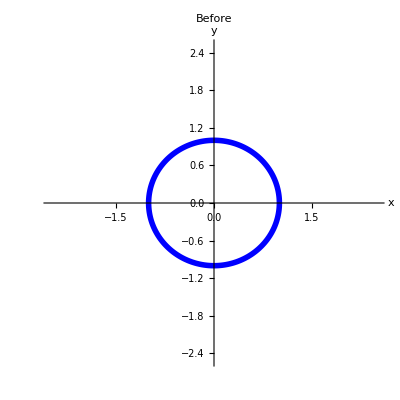

```mathematica
xstretch=1/2 Random[Integer,{1,5}];
ystretch=1/6 Random[Integer,{1,5}];
Clear[x,y,t,hitplotter,hitpointplotter,pointcolor,matrix2D];
{tlow,thigh}={0,2 π};
ranger=Max[{xstretch,ystretch,1.2}];
{x[t_],y[t_]}={Cos[t],Sin[t]};
hitplotter[matrix2D_]:=ParametricPlot[matrix2D.{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},PlotRange->{{-ranger,ranger},{-ranger,ranger}},AxesLabel->{"x","y"}];
Show[hitplotter[IdentityMatrix[2]],PlotLabel->"Before"]
```

Here's an xystretcher A:

```mathematica
A = DiagonalMatrix[{xstretch,ystretch}];
 MatrixForm[A]
```

(5/2 | 0
0 | 1/6)

Here's what you get when you hit the unit circle A

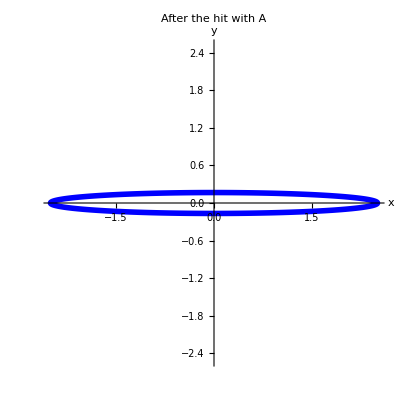

```mathematica
Clear[x,y,t,hitplotter,hitpointplotter,pointcolor,actionarrows,matrix2D]; 
{tlow,thigh}={0,2 π}; 

{x[t_],y[t_]}={Cos[t],Sin[t]}; 

pointcolor[t_]=RGBColor[0.5 (Cos[t]+1),0.5 (Sin[t]+1),0]; 

jump=(thigh-tlow)/16; 

hitplotter[matrix2D_]:=ParametricPlot[matrix2D.{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},PlotRange->{{-Max[{1.2,Max[SingularValues[A][[2]]]}],Max[{1.2,Max[SingularValues[A][[2]]]}]},{-Max[{1.2,Max[SingularValues[A][[2]]]}],Max[{1.2,Max[SingularValues[A][[2]]]}]}},AxesLabel->{"x","y"}]; 
Show[hitplotter[A],PlotLabel->"After the hit with A"]
```

Given that the area of the unit circle measures out to π square units, what does the area of the ellipse plotted above measure out to?

#### L.11)

Go with  this matrix A:

```mathematica
xstretch=1/2 Random[Integer,{1,5}];
ystretch=1/6 Random[Integer,{1,5}];
Clear[x,y,t,hitplotter,hitpointplotter,pointcolor,matrix2D];
{tlow,thigh}={0,2 π};
ranger=Max[{xstretch,ystretch,1}];
{x[t_],y[t_]}={Cos[t],Sin[t]};
hitplotter[matrix2D_]:=ParametricPlot[matrix2D.{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},PlotRange->{{-ranger,ranger},{-ranger,ranger}},AxesLabel->{"x","y"}];
A=DiagonalMatrix[{xstretch,ystretch}];
MatrixForm[A]
```

(5/2 | 0
0 | 1/6)

B is a rotation matrix whose hits rotate everything by π/6 counterclockwise radians.
Here's what you get when you hit the unit circle with B.A:

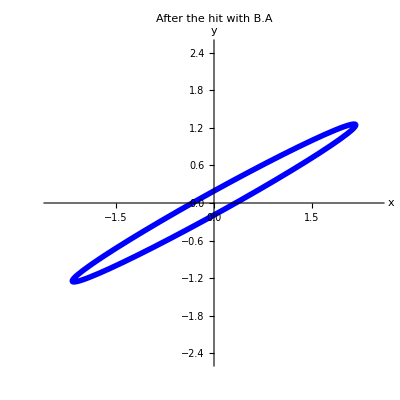

```mathematica
s = Pi/6;
{perpframe[1],perpframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
{a,c} = perpframe[1];
{b,d} = perpframe[2];
B = {{a,b},{c,d}};

 Show[hitplotter[B.A],PlotLabel->"After the hit with B.A"]
```

Given that the area of the unit circle measures out to π square units, what does the area of the ellipse plotted above measure out to?

#### L.12)

Go with  this matrix A:

```mathematica
xstretch=1/2 Random[Integer,{1,5}]; 
ystretch=1/6 Random[Integer,{1,5}]; 
Clear[x,y,t,hitplotter,hitpointplotter,pointcolor,matrix2D];
{tlow,thigh}={0,2 π};
ranger=Max[{xstretch,ystretch,1}];
{x[t_],y[t_]}={Cos[t],Sin[t]};
pointcolor[t_]=RGBColor[0.5 (Cos[t]+1),0.5 (Sin[t]+1),0];
jump=(thigh-tlow)/8;
hitplotter[matrix2D_]:=ParametricPlot[matrix2D.{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},PlotRange->{{-ranger,ranger},{-ranger,ranger}},AxesLabel->{"x","y"}];
hitpointplotter[matrix2D_]:=Table[Graphics[{pointcolor[t],PointSize[0.035],Point[matrix2D.{x[t],y[t]}]}],{t,tlow,thigh-jump,jump}];
A=DiagonalMatrix[{xstretch,ystretch}];
MatrixForm[A]
```

(3/2 | 0
0 | 1/2)

B is the rotation matrix whose hits rotate everything by π/4 counterclockwise radians.
Here's what you get when you hit the unit circle with A.B:

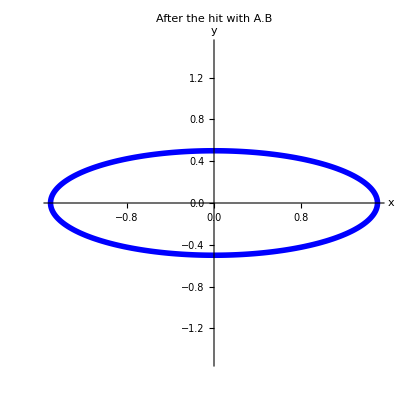

```mathematica
s = Pi/4;
{perpframe[1],perpframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
{a,c} = perpframe[1];
{b,d} = perpframe[2];
B = {{a,b},{c,d}};

 Show[hitplotter[A.B],PlotLabel->"After the hit with A.B"]
```

Given that the area of the unit circle measures out to π square units, what does the area of the ellipse plotted above measure out to?
Why is this ellipse not tilted?

#### L.13)

For a given 2D matrix A, the inverse matrix  A^-1is the matrix you hit with to undo whatever a hit with A did.
For instance, when you hit with this stretcher matrix A:

```mathematica
{xstretch,ystretch}={Random[Integer,{4,6}],Random[Integer,{1,3}]}; 
stretcher=DiagonalMatrix[{xstretch,ystretch}]; 
MatrixForm[stretcher]
```

(5 | 0
0 | 2)

The numbers a, b, c and d that make
          A^-1=(a | b
c | d)
are
           a = .......................   b = .......................
           c =........................    d = .......................

#### L.14)

Hits with the following matrix rotate everything about {0,0} by s counterclockwise radians:

```mathematica
Clear[s,rotator,perpframe]; 
{perpframe[1],perpframe[2]}=N[{{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}}]; 
{a,c}=perpframe[1]; 
{b,d}=perpframe[2]; 
rotator[s_]={{a,b},{c,d}};
MatrixForm[rotator[s]]
```

(Cos[s] | -1. Sin[s]
Sin[s] | Cos[s])

The entries a, b, c and d that make
          rotator[s]^-1=(a | b
c | d)
are
           a = .......................   b = .......................
           c =........................    d = .......................

#### L.15)

Remembering that 
         shear[a].shear[b]=shear[a+b]
and that 
         shear[0] =   (1 | 0
0 | 1),
come up with the b that makes
          shear[a]^-1 = shear[b].

#### L.16)

Given two invertible matrices A and B, the inverse of A.B is
a)  A^-1. B^-1
b)  B^-1. A^-1.
My choice is ..............

#### L.17)

Here's the square with corners at {0,0}, {1,0}, {1,1} and {0,1} with lots of points inside:

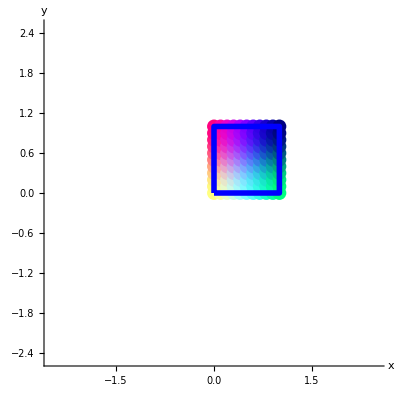

```mathematica
jump=0.1;
Clear[parallelogramplotter,basepoint,side1,side2,pointcolor];
ranger=2.5;
pointcolor[r_,t_]=RGBColor[0.5 (Cos[π t]+1),0.5 (Cos[π r]+1),0.5 (Sin[π t]+1)];
parallelogramplotter[basepoint_,side1_,side2_]:={Table[Graphics[{PointSize[0.025],pointcolor[r,t],Point[basepoint+t side1+r side2]}],{t,0,1,jump},{r,0,1,jump}],Graphics[{Thickness[0.01],Blue,Line[{basepoint,basepoint+side1,basepoint+side1+side2,basepoint+side2,basepoint}]}]};
basepoint={0,0};
squareside1={1,0};
squareside2={0,1};
Show[parallelogramplotter[basepoint,squareside1,squareside2],PlotRange->{{-ranger,ranger},{-ranger,ranger}},Axes->True,AxesLabel->{"x","y"}]
```

Here's a random 2D matrix A:

```mathematica
A=N[{{Random[Real,{0.4,1.2}],-Random[Real,{0.4,1.5}]},{Random[Real,{0.4,1.2}],Random[Real,{0.5,1.5}]}},3]; 

MatrixForm[A]
```

(0.494852 | -1.20137
1.08342 | 0.931353)

Here's what you get when you hit this square and the points inside with A:

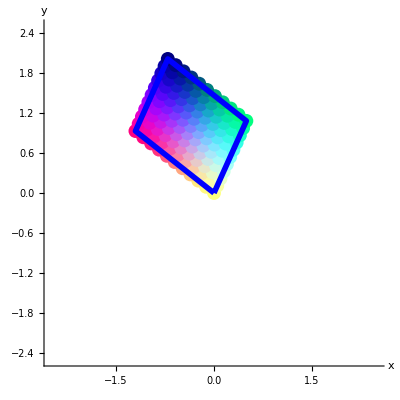

```mathematica
basepoint={0,0};
squareside1={1,0};
squareside2={0,1};
hitsquare=Show[parallelogramplotter[A.basepoint,A.squareside1,A.squareside2],PlotRange->{{-ranger,ranger},{-ranger,ranger}},Axes->True,AxesLabel->{"x","y"}]
```

Look at A again:

```mathematica
MatrixForm[A]
```

(0.494852 | -1.20137
1.08342 | 0.931353)

Use what you see to identify the vectors that define the parallelogram.

#### L.18)

Here is a cleared 2D matrix A:

```mathematica
Clear[a,b,c,d];
A={{a,b},{c,d}};
MatrixForm[A]
```

(a | b
c | d)

Here's another 2D matrix B:

```mathematica
B= {{Random[Integer,{1,4}],Random[Integer,{1,4}]},
		   {Random[Integer,{1,4}],Random[Integer,{1,4}]}};
MatrixForm[B]
```

(2 | 3
3 | 4)

When you calculate A.B, you get another 2D matrix 
                (x | y
z | w).
 Your job is to write down what the values of x,y,z and w are.
 x = .....................................................
 y = .....................................................
 z = .....................................................
 w = .....................................................

#### L.19)

Here are calculations of A.B and B.A for two random 2D matrices A and B:

```mathematica
A={{Random[Real,{-8,8}],Random[Real,{-8,8}]},{Random[Real,{-8,8}],Random[Real,{-8,8}]}};
B={{Random[Real,{-8,8}],Random[Real,{-8,8}]},{Random[Real,{-8,8}],Random[Real,{-8,8}]}};
MatrixForm[A.B]
MatrixForm[B.A]
```

(-48.7066 | 7.98566
-13.9042 | -5.39025)

(-29.9256 | -26.1363
-13.3823 | -24.1713)

Does the outcome surprise you? 
Why or why not?